```mathematica
(*Similar to former cases, use Runge-Kutta to find the period shifting map(PSM) of the vector field: *)
X[k_][{x_,v_,t_}]:={v,-Sin[x]+k Cos[t],1}
```

```mathematica
Algo[k_,h_][xvt_]:=xvt+h X[k][xvt+h/2 X[k][xvt]]
```

```mathematica
Algo[k,h][{xvt[[1]],xvt[[2]],xvt[[3]]}]
```

Part::partd: Part specification xvt⟦1⟧ is longer than depth of object.

Part::partd: Part specification xvt⟦2⟧ is longer than depth of object.

Part::partd: Part specification xvt⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{xvt⟦1⟧+h (xvt⟦2⟧+1/2 h (k Cos[xvt⟦3⟧]-Sin[xvt⟦1⟧])),xvt⟦2⟧+h (k Cos[h/2+xvt⟦3⟧]-Sin[xvt⟦1⟧+1/2 h xvt⟦2⟧]),h+xvt⟦3⟧}

```mathematica
Algo=Compile[{ k,h,{xvt,_Real,1}} ,
{Mod[xvt⟦1⟧+h (xvt⟦2⟧+1/2 h (k Cos[xvt⟦3⟧]-Sin[xvt⟦1⟧])),2π],xvt⟦2⟧+h (k Cos[h/2+xvt⟦3⟧]-Sin[xvt⟦1⟧+1/2 h xvt⟦2⟧]),h+xvt⟦3⟧}];
```

```mathematica
PSM=Compile[{k,{ndiv,_Integer},{xv,_Real,1}},
Take[Nest[Algo[k,(2π)/ndiv,#]&,Append[xv,0],Abs[ndiv]], 2]
];
```

```mathematica
OrbPSM[k_,ndiv_,nit_,xv_]:=NestList[ PSM[k,ndiv,#]&,xv,nit]
```

### 1. Phase portraits

```mathematica
GOrbPSM[k_,ndiv_,nit_][xv_]:=ListPlot[OrbPSM[k,ndiv,nit,xv],PlotRange->{{0,2π},{-3,3}},PlotStyle->PointSize[.005],Frame->True]
```

```mathematica
(*For simplicity, define the phase portrait with parameter k and lst (a list of initial points): *)
PhP[k_,ndiv_,nit_,lst_]:=Map[GOrbPSM[k,ndiv,nit],lst];
```

```mathematica
(*k=0 : *)
```

```mathematica
lst1={{π,.01},{π,-.01},{π/2,.01},{π/4,.01},{π/20,.01},{0,2.5},{0,-2.5}};
```

```mathematica
php1=Labeled[Show[PhP[0,400,1000,lst1]],Style["k=0"]];
```

```mathematica
(*k=0.05 : *)
```

```mathematica
lst2={{π,.01},{π,-.01},{π/2,.01},{π/4,.01},{π/20,.01},{0,2.5},{0,-2.5}};
```

```mathematica
php2=Labeled[Show[PhP[0.05,400,1000,lst2]],Style["k=0.05"]];
```

```mathematica
(*k=0.3 : *)
```

```mathematica
lst3={{π,.01},{π,-.01},{0,2.6},{0,-2.6},{-2.4,0},{-0.51,0},{-0.6,0},{-2.2,0},{-1.6,0}};
```

```mathematica
php3=Labeled[Show[PhP[0.3,400,1000,lst3]],Style["k=0.3"]];
```

```mathematica
(*k=0.5 : *)
```

```mathematica
lst4={{π,.01},{π,1.6},{π,-1.6},{-2.5,0},{-2,0},{0,2.7},{0,-2.7}};
```

```mathematica
php4=Labeled[Show[PhP[0.5,400,2000,lst4]],Style["k=0.5"]];
```

```mathematica
(*k=0.7 : *)
```

```mathematica
lst5={{π,.01},{-2.1,0},{π,2.1},{π,2.2},{π,2.4},{π,-2.1},{π,-2.2},{π,-2.4},{2.8,1.4},{2.8,-1.4}};
```

```mathematica
php5=Labeled[Show[PhP[0.7,400,2000,lst5]],Style["k=0.7"]];
```

```mathematica
(*k=1 : *)
```

```mathematica
lst6={{π,.01},{0.4,0.7},{0.4,-0.7},{-2.4,0},{-π,-2.5},{-π,2.5},{-π,-2.6},{-π,2.6}};
```

```mathematica
php6=Labeled[Show[PhP[1,400,2000,lst6]],Style["k=1"]];
```

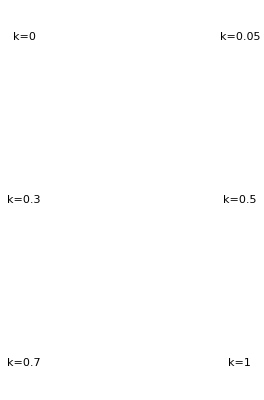

```mathematica
GraphicsGrid[{{php1,php2},{php3,php4},{php5,php6}}]
```

```mathematica
(*The pictures shows that the chaotic region increases with k. *)
```

### 2. Stable and unstable manifolds (homoclinic tangles)

We use the Lambda lemma to find the unstable and stable manifolds. 
Here, for example, I take k=0.05, 0.3, 0.7 respectively. 
First, estimate the fixed point by plotting ||Subscript[Ψ, k](x,0)-(x,0)||, which is close to (π,0).

#### 2.1 k = 0.05

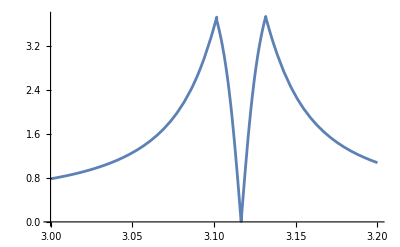

```mathematica
Plot[Norm[PSM[.05,100,{x,0}]-{x,0}] , {x,3,3.2}]
```

```mathematica
(*The x-coordinaate of fixed point is in (3.11,3.12). *)
```

```mathematica
pts1=Table[{RandomReal[{3.11,3.12}],RandomReal[{-0.01,0.01}]},10000];
```

```mathematica
unst11=Map[PSM[0.05,200,#]&,pts1];
```

```mathematica
unst12=Map[PSM[0.05,200,#]&,unst11];
```

```mathematica
unst13=Map[PSM[0.05,200,#]&,unst12];
```

```mathematica
gunst1=ListPlot[Join[unst11,unst12,unst13], PlotStyle->{Red,PointSize[.001]},PlotRange->{{0,2π},{-3,3}}];
```

```mathematica
st11=Map[PSM[0.05,-200,#]&,pts1];
```

```mathematica
st12=Map[PSM[0.05,-200,#]&,st11];
```

```mathematica
st13=Map[PSM[0.05,-200,#]&,st12];
```

```mathematica
gst1=ListPlot[Join[st11,st12,st13], PlotStyle->{Blue,PointSize[.001]},PlotRange->{{0,2π},{-3,3}}];
```

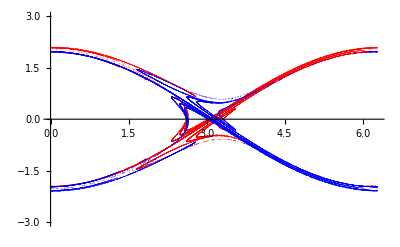

```mathematica
Show[gunst1,gst1]
```

#### 2.2 k = 0.3

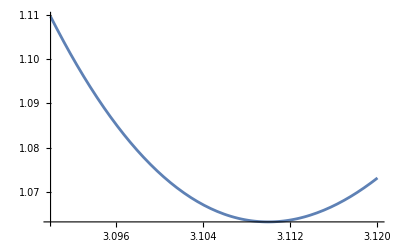

```mathematica
Plot[Norm[PSM[0.3,100,{x,0}]-{x,0}] , {x,3.09,3.12}]
```

```mathematica
(*The x-coordinaate of fixed point is in (3.105,3.115). *)
```

```mathematica
pts2=Table[{RandomReal[{3.105,3.115}],RandomReal[{-0.01,0.01}]},10000];
```

```mathematica
unst21=Map[PSM[0.3,200,#]&,pts2];
```

```mathematica
unst22=Map[PSM[0.3,200,#]&,unst21];
```

```mathematica
unst23=Map[PSM[0.3,200,#]&,unst22];
```

```mathematica
unst24=Map[PSM[0.3,200,#]&,unst23];
```

```mathematica
unst25=Map[PSM[0.3,200,#]&,unst24];
```

```mathematica
gunst2=ListPlot[Join[unst21,unst22,unst23,unst24,unst25], PlotStyle->{Red,PointSize[.001]},PlotRange->{{0,2π},{-3,3}}];
```

```mathematica
st21=Map[PSM[0.3,-200,#]&,pts2];
```

```mathematica
st22=Map[PSM[0.3,-200,#]&,st21];
```

```mathematica
st23=Map[PSM[0.3,-200,#]&,st22];
```

```mathematica
st24=Map[PSM[0.3,-200,#]&,st23];
```

```mathematica
st25=Map[PSM[0.3,-200,#]&,st24];
```

```mathematica
gst2=ListPlot[Join[st21,st22,st23,st24,st25], PlotStyle->{Blue,PointSize[.001]},PlotRange->{{0,2π},{-3,3}}];
```

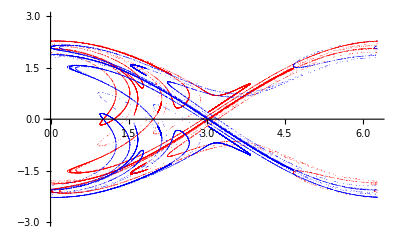

```mathematica
Show[gunst2,gst2]
```

#### 2.3 k = 0.7

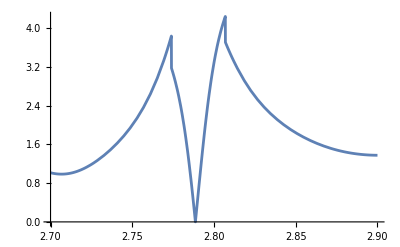

```mathematica
Plot[Norm[PSM[0.7,100,{x,0}]-{x,0}] , {x,2.7,2.9}]
```

```mathematica
(*The x-coordinaate of fixed point is in (2.75,2.85). *)
```

```mathematica
pts3=Table[{RandomReal[{2.75,2.85}],RandomReal[{-0.01,0.01}]},10000];
```

```mathematica
unst31=Map[PSM[0.7,200,#]&,pts3];
```

```mathematica
unst32=Map[PSM[0.7,200,#]&,unst31];
```

```mathematica
unst33=Map[PSM[0.7,200,#]&,unst32];
```

```mathematica
gunst3=ListPlot[Join[unst31,unst32,unst33], PlotStyle->{Red,PointSize[.001]},PlotRange->{{0,2π},{-3,3}}];
```

```mathematica
st31=Map[PSM[0.7,-200,#]&,pts3];
```

```mathematica
st32=Map[PSM[0.7,-200,#]&,st31];
```

```mathematica
st33=Map[PSM[0.7,-200,#]&,st32];
```

```mathematica
gst3=ListPlot[Join[st31,st32,st33], PlotStyle->{Blue,PointSize[.001]},PlotRange->{{0,2π},{-3,3}}];
```

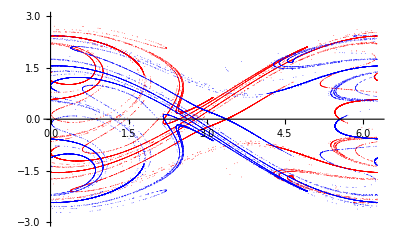

```mathematica
Show[gunst3,gst3]
```

```mathematica
(*It can be seen from the pictures that the homoclinic tangle becomes larger as k increases. *)
```

### 3. Investigation on Lyapunov indicator

```mathematica
(*To calculate Lyapunov indicator, we need to consider its tangent lift. First calculate the Jacobian matrix of X: *)
```

```mathematica
JacX=D[X[k][{x,v,t}],{{x,v,t}}];
```

```mathematica
JX[k_][{x_,v_,t_}]=JacX;
```

```mathematica
(*Then the tangent dynamics with parameter k, u being the tangent vector*)
```

```mathematica
TGX[k_][{xvt_,u_}]:={X[k][xvt],JX[k][xvt].u};
```

```mathematica
TgAlgo[k_,h_][{xvt_,u_}]:={xvt,u}+h TGX[k][{xvt,u}+h/2 TGX[k][{xvt,u}]]
```

```mathematica
TgOrb[k_,h_,nit_][{xvt_,u_}]:=NestList[TgAlgo[k,h],{xvt,u},nit]
```

```mathematica
(*The Lyapunov indicator is calculated as: *)
LCE[k_,h_,nit_][{xvt_,u_}]:=Drop[Log[Map[Norm,Transpose[TgOrb[k,h,nit][{xvt,u}]][[2]]]],1]/(.01 Range[nit])
```

```mathematica
(*For k=0.3, take two points (π,0.1)(in chaotic region) and (0,-2.6)(in regular region) respectively: *)
```

```mathematica
lce1c=LCE[0.3,0.1,20000][{{π,0.1,0},{.1,.1,.1}}];
```

```mathematica
lce1r=LCE[0.3,0.1,20000][{{0,-2.6,0},{.1,.1,.1}}];
```

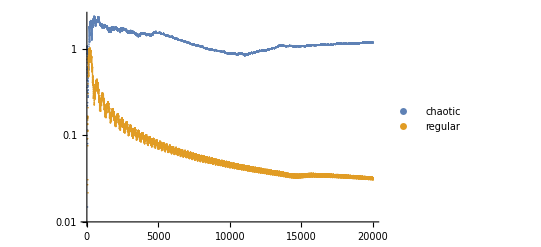
-Graphics-Log Plot, k=0.3

```mathematica
Labeled[ListLogPlot[{lce1c,lce1r},PlotLegends->{"chaotic","regular"}],"Log Plot, k=0.3"]
```

```mathematica
(*For k=0.5, take two points (π,0.1)(in chaotic region) and (0,-2.5)(in regular region) respectively: *)
```

```mathematica
lce2c=LCE[0.5,0.1,20000][{{π,0.1,0},{.1,.1,.1}}];
```

```mathematica
lce2r=LCE[0.5,0.1,20000][{{0,2.7,0},{.1,.1,.1}}];
```

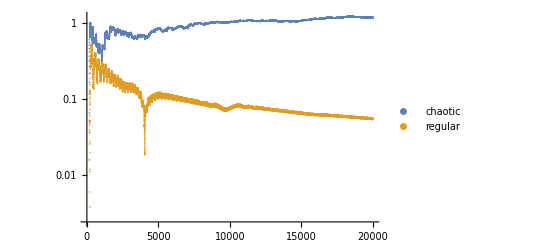
-Graphics-Log Plot, k=0.5

```mathematica
Labeled[ListLogPlot[{lce2c,lce2r},PlotLegends->{"chaotic","regular"}],"Log Plot, k=0.5"]
```

```mathematica
(*For k=0.7, take two points (π,0.1)(in chaotic region) and (2.8,1.4),(π,2.1)(in regular region) respectively: *)
```

```mathematica
lce3c=LCE[0.01,0.1,20000][{{π,0.1,0},{.1,.1,.1}}];
```

```mathematica
lce3r1=LCE[0.01,0.1,20000][{{2.8,1.4,0},{.1,.1,.1}}];
```

```mathematica
lce3r2=LCE[0.01,0.1,20000][{{π,2.1,0},{.1,.1,.1}}];
```

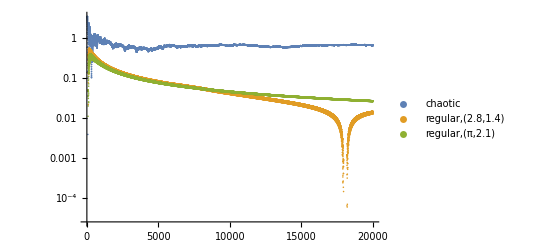
-Graphics-Log Plot, k=0.7

```mathematica
Labeled[ListLogPlot[{lce3c,lce3r1,lce3r2},PlotLegends->{"chaotic","regular,(2.8,1.4)","regular,(π,2.1)"}],"Log Plot, k=0.7"]
```

```mathematica
(*Discontinuity occurs for initial condition (2.8,1.4). In the phase portrait, this intial condition forms a "closed circle".  *)
```

```mathematica
(*Lyapunov indicator seems not to exist for initial data that are in the regular region. Therefore, only those for the chaotic ones need to be compared: *)
```

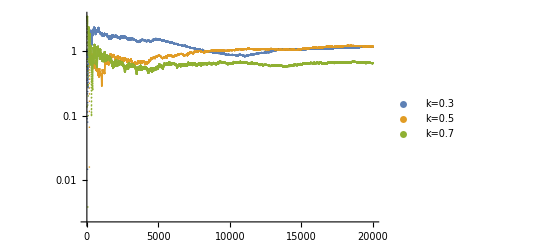
-Graphics-Log plot for different k's

```mathematica
Labeled[ListLogPlot[{lce1c,lce2c,lce3c},PlotLegends->{"k=0.3","k=0.5","k=0.7"}],"Log plot for different k's"
]
```

```mathematica
(*It seems no feature can be deduced from the picture. To have a better look, I try to approximate LCE by average of points of the last quater, with fixed time of iteration, stepsize, with k in [0.05,10]: *)
```

```mathematica
LCEapr[xvt_,u_][k_]:=Mean[Drop[LCE[k,0.1,20000][{xvt,u}],15000]]
```

```mathematica
lst=0.05Range[200];
```

```mathematica
gr=Map[LCEapr[{π,0.01,0},{.1,.1,.1}],lst];
```

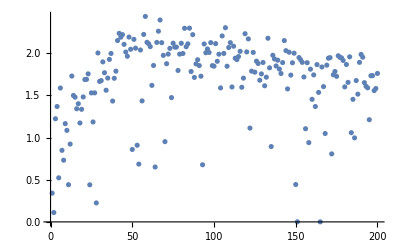

```mathematica
ListPlot[gr,Ticks->None]
```

```mathematica
(*There seems to be an overall trend that "first increase rapidly then decrease slowly". *)
```